```mathematica
ClearAll["`*",Subscript,Derivative]
```

```mathematica
(*s=0.0001;
θ=π;
α=(9 π)/8;*)
A=ⅇ^(ⅈ θ) Tan[α/2];
Subscript[X, 1]=1/2 s (Cosh[r]+ⅇ^(ⅈ θ) Sinh[r]);
Subscript[X, 2]=1/2 (-s) (Cosh[r]+ⅇ^(-ⅈ θ) Sinh[r]);
NN[r_]=√2 Sinh[r] ((1+Abs[A]^2) (Sinh[r]^2+s^2/4)+(1-Abs[A]^2) (Subscript[X, 1] Subscript[X, 2] (1+2 Sinh[r]^2)-Subscript[X, 2]^2 ⅇ^(ⅈ θ) Sinh[r] Cosh[r]-Subscript[X, 1]^2 ⅇ^(-ⅈ θ) Sinh[r] Cosh[r]+Sinh[r]^2) ⅇ^(-1/2 s^2 Abs[Cosh[r]+ⅇ^(ⅈ θ) Sinh[r]]^2))^(-1/2);
```

```mathematica
FullSimplify[NN@r,α∈Reals&&Tan[α/2]∈Reals&&θ∈Reals]
FullSimplify[%/.s->0]
Simplify[%,r>0]
```

(4 Sinh[r])/(√(Sec[α/2]^2 (2 (s^2+4 Sinh[r]^2)+ⅇ^(-ⅈ θ-1/2 s^2 Abs[Cosh[r]+ⅇ^(ⅈ θ) Sinh[r]]^2) Cos[α] (-2 ⅇ^(ⅈ θ) (2-2 Cosh[2 r]+s^2 Cosh[4 r])-s^2 Sinh[4 r]-ⅇ^(2 ⅈ θ) s^2 Sinh[4 r]))))

Csch[r] √(Sinh[r]^2)

1

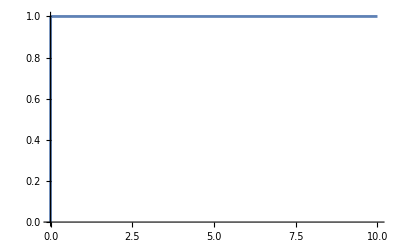

```mathematica
Plot[NN[r]/.{s->.0001,θ->π,α->9π/8},{r,0,10},PlotRange->All]
```